```mathematica
(* The first step in this process is to create a grid of points where the vector field will be approximated. If you reduce "Pts" too agressively, you normally get a terrible result. Depending on the resolution of your screen, you may need to expand the grid to make it not look weird (The screen samples at the wrong frequency and creates bands)*)
```

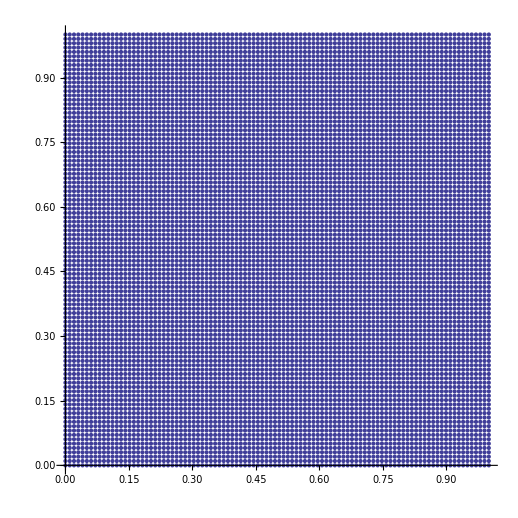

```mathematica
pts = 100;
nx = N[Range[0,1,1/(pts-1)]];
grid = Flatten[Outer[List,nx,nx],1];
ListPlot[grid, AspectRatio -> 1, PlotRange-> {{0,1},{0,1}}]
```

```mathematica
(* Next, variables for the x-velocity, y-velocity, and pressure will be made into a table corresponding to each point in the grid*)
```

```mathematica
nL=Length[grid];
varsU=Table[Unique[u$],{nL}];
varsV=Table[Unique[v$],{nL}];
varsP=Table[Unique[p$],{nL}];
```

```mathematica
(* This next step is quite interesting. Basically, using the built in NDSolve Function, the matricies used to compute the finite difference derivatives for different equations are found. This basically allows the 30000 equations necessary to solve the 100*100 grid to be generated very quickly *)
```

```mathematica
opt = "DifferenceOrder"->4;
dfdx = NDSolve`FiniteDifferenceDerivative[{1,0},{nx,nx}, opt]["DifferentiationMatrix"] ; 
dfdy = NDSolve`FiniteDifferenceDerivative[{0,1},{nx,nx}, opt]["DifferentiationMatrix"] ; 
d2fdx2 = NDSolve`FiniteDifferenceDerivative[{2,0},{nx,nx}, opt]["DifferentiationMatrix"] ; 
d2fdy2 = NDSolve`FiniteDifferenceDerivative[{0,2},{nx,nx}, opt]["DifferentiationMatrix"] ;
```

```mathematica
(* Below are the differential equations used for the by the Navier-Stokes Model. They are from wikipedia*)
```

```mathematica
Rey = 100;

eqnsU = varsU*(dfdx.varsU) + varsV*(dfdy.varsU) + dfdx.varsP - (1/Rey)*((d2fdx2 + d2fdy2).varsU) ; 

eqnsV = varsU*(dfdx.varsV) + varsV*(dfdy.varsV) + dfdy.varsP - (1/Rey)*((d2fdx2 + d2fdy2).varsV) ; 

eqnsCont = dfdx.varsU + dfdy.varsV ;
```

```mathematica
(* Below are the boundaries. I have several different values for "boundaries" that can be commented in or out depending on what shape you want to model. Basically, I am using the edges to define boundary condition velocities, and using "boundaries" to define the 0 velocity regions where the solid objects are. Theoretically, I could make "boundaries" hollow but doing it this way seems to work better *)
```

```mathematica
edges = DeleteDuplicates@Flatten[Position[grid,#]& /@ {{0.,y_},{1.,y_},{x_,0.},{x_,1.}}] ;
bound2=Join[Table[Table[(r-1)*pts+c,{r,2*pts/10,3*pts/10}],{c,3*pts/10,7*pts/10}],Table[Table[(r-1)*pts+c,{r,5*pts/10,7*pts/10}],{c,3*pts/10,7*pts/10}]];
(*boundaries=Flatten[bound2];*)
boundaries=DeleteDuplicates[Table[If[(grid[[i,1]]-.5)^2/(.005)+(grid[[i,2]]-.5)^2/(.15)<1 && grid[[i,1]]<.5, i,1], {i,1, Length[grid]}]][[2;;All]]; (* half or whole wing*)
(*boundaries= Join[DeleteDuplicates[Table[If[(grid[[i,1]]-.8)^2/(.05)+(grid[[i,2]]-.5)^2/(.15)<1 && grid[[i,1]]<.8, i,1], {i,1, Length[grid]}]][[2;;All]],DeleteDuplicates[Table[If[(grid[[i,1]]-.2)^2/(.05)+(grid[[i,2]]-.5)^2/(.15)<1 && grid[[i,1]]>.2, i,1], {i,1, Length[grid]}]][[2;;All]]];*) (* two half circles *)
topBndry = Flatten@Position[grid,{x_,1.}]  ;
bndryComp = Complement[boundaries,topBndry];
```

```mathematica
(*Here, the x and y velocity componets on the edges are defined. By making this not in a straight line, the angle of attack can be changed. Keep in mind that large velocites make everything explode when you get to FindRoot below*)
xvel=0;
yvel=1;
```

```mathematica
(* these two define the non-moving regions*)
eqnsU[[boundaries]] = varsU[[boundaries]] ; 
eqnsV[[boundaries]]= varsV[[boundaries]] ;
(* These burn the x- and y- parts of the velocity onto the edges throughout the simulation*)
eqnsU[[edges]]=varsU[[edges]]-xvel; 
eqnsV[[edges]] = varsV[[edges]]-yvel;
eqnsCont[[topBndry[[1]] ]] = varsP[[topBndry[[1]] ]] ;
```

```mathematica
govExpr=Join[eqnsU,eqnsV,eqnsCont];
allVars = Join[varsU, varsV, varsP];
Length /@ {govExpr, allVars}
```

{30000,30000}

```mathematica
(* this find-root just solves the system, it takes a long time. Often you get weird errors if you try new shapes. If so, just hope that the plot that comes out below works. If it does not, try smoothing out your shape (or reducing the grid size) *)
```

```mathematica
sol = allVars/.FindRoot[govExpr,Thread[{allVars,1}]] ;
```

```mathematica
{usoltemp,vsoltemp,psoltemp} = Partition[sol,nL] ;
```

```mathematica
(* This code produces a pretty plot that takes a really really long time to compute and does not show the direction of the flow. Leave it commented out for now. *)
```

```mathematica
(*
usol = Interpolation@Join[grid,Transpose@List@usoltemp,2] ;
vsol = Interpolation@Join[grid,Transpose@List@vsoltemp,2] ; 
psol = Interpolation@Join[grid,Transpose@List@psoltemp,2] ; 
LineIntegralConvolutionPlot[{{usol[x,y],vsol[x,y]},{"noise",1000,1000}},{x,0,1},{y,0,1},LineIntegralConvolutionScale->3,
ColorFunction->"RoseColors", PlotLabel -> Style[Text["Flow at Reynolds number 100"],18]] *)
```

```mathematica
(* This just takes the output of the FindRoot and converts it into something that works for ListVectorPlot*)
data=Table[{grid[[a]],{usoltemp[[a]],vsoltemp[[a]]}},{a,1,Length[grid]}];
```

```mathematica
pressuredata=Table[{grid[[a]],psoltemp[[a]]},{a,1,Length[grid]}];
```

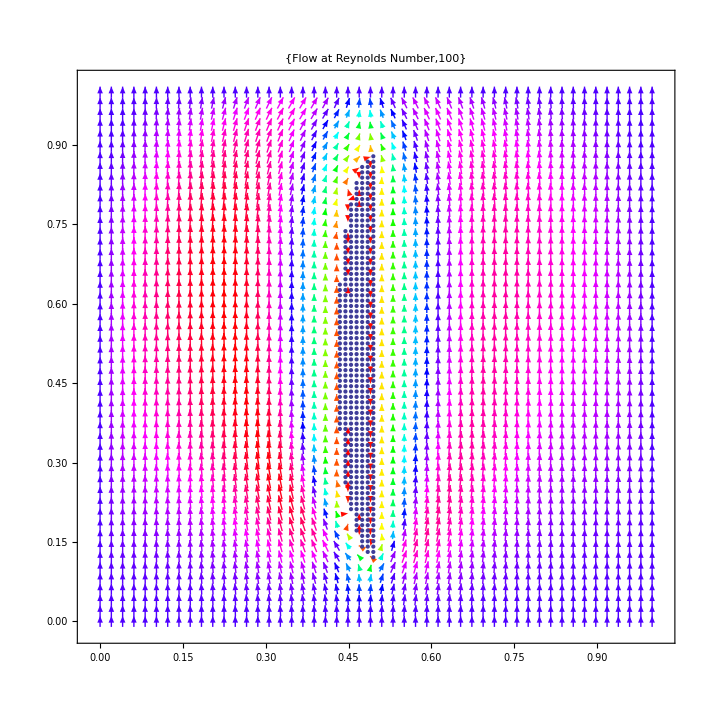

```mathematica
(* This just makes the plot, to change the number of vectors shown, change "VectorPoints". 50 Normally works quite well. 100 makes something like a heatmap(Magnitudes are velocities) *)
Show[ListVectorPlot[data,VectorPoints->50,VectorColorFunction->Hue,PlotLabel-> {Text["Flow at Reynolds Number"], Rey}],ListPlot[grid[[boundaries]],PlotRange-> {{0,1},{0,1}},AspectRatio->1]]
```

Sources :
 Wikipedia
 http://blog.wolfram.com/2013/07/09/using-mathematica-to-simulate-and-visualize-fluid-flow-in-a-box/